```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/phase_space_stoc/PDF_zetaR/math"]
```

/Users/yuichirotada/Documents/Univ/phase_space_stoc/PDF_zetaR/math

### Setup

```mathematica
B[NN_]=(2π xf)/H-(2π dotx0)/(3 H^2)(1-E^(-3NN));
NB[x_]=InverseFunction[B][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/3 Log[(2 dotx0 π)/(2 dotx0 π+3 H^2 x-6 H π xf)]

```mathematica
H=10^-8;
calPf=1/(2ϵfs)(H/(2π))^2
```

1/(80000000000000000 π^2 ϵfs)

```mathematica
ϵf=ϵfs/.Solve[calPf==10^-3,ϵfs][[1]];ϵf//N
```

1.26651×10^-15

```mathematica
ϵf
```

1/(80000000000000 π^2)

```mathematica
8 10^13
```

80000000000000

```mathematica
ϵi=10^-2;
```

```mathematica
Nf=Log[ϵi/ϵf]/6;Nf//N
```

4.94956

```mathematica
dotx0=dotx0s/.Solve[ϵi==dotx0s^2/(2 H^2),dotx0s][[2]]
dotxf=dotxfs/.Solve[ϵf==dotxfs^2/(2 H^2),dotxfs][[2]]
```

1/(500000000 √2)

1/(200000000000000 √10 π)

```mathematica
5 10^8
2 10^14
```

500000000

200000000000000

```mathematica
xf=(dotx0-dotxf)/(3H);xf//N
```

0.0471404

```mathematica
xf/(H/(2π))//N
```

2.96192×10^7

```mathematica
B[NN_]=(2π xf)/H-(2π dotx0)/(3 H^2)(1-E^(-3NN))//Simplify
P0[x_,NN_]=1/Sqrt[2π NN] Exp[-x^2/(2NN)];
```

10/3 √2 (-√5+2000000 ⅇ^(-3 NN) π)

```mathematica
g1[NN_]=(B[NN]/NN-2B'[NN])P0[B[NN],NN]//Simplify
g2[N1_,N2_]=(2B'[N1]-(B[N1]-B[N2])/(N1-N2))P0[B[N1]-B[N2],N1-N2]//Simplify
```

(ⅇ^(-3 NN-(100 (√5-2000000 ⅇ^(-3 NN) π)^2)/(9 NN)) (-10 √5 ⅇ^(3 NN)+20000000 (π+6 NN π)))/(3 NN^(3/2) √π)

(20000000 ⅇ^(-3 N1-3 N2-(400000000000000 ⅇ^(-6 (N1+N2)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

### Volterra

```mathematica
G1[N1_,N2_]=g2[N1,N2];
```

```mathematica
f1[NN_]:=g1[NN]+NIntegrate[g1[Np]G1[NN,Np],{Np,0,NN}]
```

```mathematica
f1[5]
```

-0.0520354

```mathematica
f1List=ParallelTable[{NN,f1[NN]//Quiet},{NN,4,8,1/10}];//AbsoluteTiming
```

{0.141571,Null}

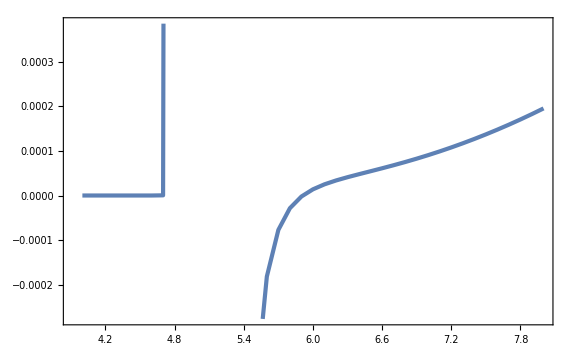

```mathematica
ListPlot[f1List]
```

```mathematica
G2[N1_,N2_]:=NIntegrate[g2[N1,Np]G1[Np,N2],{Np,N2,N1}]
```

```mathematica
G2[7,7-1/100]
```

0.00226944

```mathematica
G2List=Flatten[ParallelTable[{{N1,N2},If[N1<N2,0,G2[N1,N2]//Quiet]},{N1,4,8,1/100},{N2,4,8,1/100}],1];//AbsoluteTiming
```

$Aborted

```mathematica
G2int[N1_,N2_]=Interpolation[Flatten[G2List,1],InterpolationOrder->1][N1,N2];
```

```mathematica
G2List[[1,1]]
```

{{4,4},0.}

```mathematica
Normal[Series[1/Sqrt[x],{x,0,1}]]
```

1/(√x)

### Numerical Integrate

```mathematica
DN=1/200(*1/100*);
Nmin=0;
Nmax=8;
NList=Table[NN,{NN,Nmin,Nmax,DN}];
Length[NList]
```

1601

```mathematica
Delta=ParallelTable[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2[NList[[i]],Np],{Np,NList[[i]]-DN,NList[[i]]}]]//Quiet,N[DN/2 g2[NList[[i]],NList[[j]]-DN/2]]//Quiet]],{i,Length[NList]},{j,Length[NList]}];//AbsoluteTiming
```

{261.212,Null}

```mathematica
FPFTList=Table[0,{i,Length[NList]}];
```

```mathematica
FPFTList[[1]]={NList[[1]],0};
FPFTList[[2]]={NList[[2]],g1[NList[[2]]](1-Delta[[2,2]])^-1}//Quiet;
For[i=3,i≤Length[FPFTList],i++,
FPFTList[[i]]={NList[[i]],(1-Delta[[i,i]])^-1(g1[NList[[i]]]+ParallelSum[FPFTList[[j,2]](Delta[[i,j]]+Delta[[i,j+1]])//Quiet,{j,2,i-1}])}//Quiet;]//AbsoluteTiming
```

{180.311,Null}

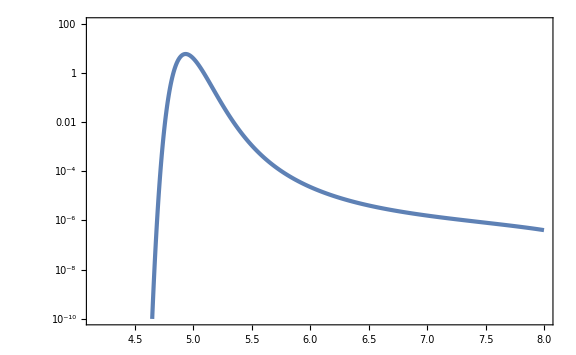

```mathematica
ListLogPlot[FPFTList,PlotRange->{10^-10,100}]
```

```mathematica
FPFTint[NN_]=Interpolation[FPFTList,InterpolationOrder->1][NN];
```

```mathematica
NIntegrate[FPFTint[NN],{NN,Nmin,Nmax}]
Nmean=NIntegrate[NN FPFTint[NN],{NN,Nmin,Nmax}]
varZ=NIntegrate[(NN-Nmean)^2 FPFTint[NN],{NN,Nmin,Nmax}]
Z3=NIntegrate[(NN-Nmean)^3 FPFTint[NN],{NN,Nmin,Nmax}]
Z4=NIntegrate[(NN-Nmean)^4 FPFTint[NN],{NN,Nmin,Nmax}]-3 varZ^2
fNL=5/18 Z3/varZ^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.953}. NIntegrate obtained 1.00525 and 0.0000209885 for the integral and error estimates.

1.00525

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.953}. NIntegrate obtained 4.98305 and 0.000103278 for the integral and error estimates.

4.98305

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.81238}. NIntegrate obtained 0.00649927 and 5.63536×10^-7 for the integral and error estimates.

0.00649927

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.828}. NIntegrate obtained -0.0000482231 and 8.31801×10^-8 for the integral and error estimates.

-0.0000482231

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.828}. NIntegrate obtained 0.000213201 and 1.73466×10^-8 for the integral and error estimates.

0.000086479

-0.31712

```mathematica
FPFTLogCut=Map[{#[[1]],Log[#[[2]]]}&,Select[FPFTList,6<#[[1]]&]];
```

```mathematica
expfit=FindFit[FPFTLogCut,a-b(x-Nmean),{a,b},x]
exp3fit=FindFit[FPFTLogCut,a-b(x-Nmean)-3Log[x-Nmean],{a,b},x]
```

{a→-9.54019,b→1.7916}

{a→-10.7297,b→0.224297}

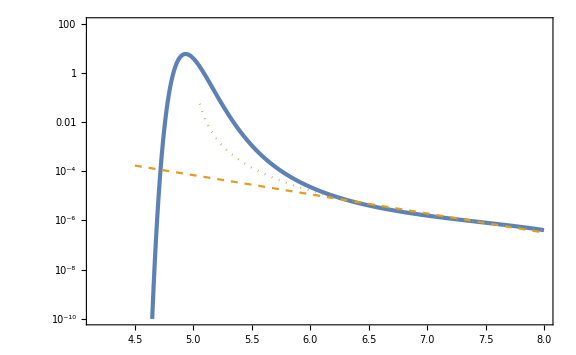

```mathematica
Show[ListLogPlot[FPFTList,PlotRange->{10^-10,100}],LogPlot[{Exp[a] Exp[-b (x-Nmean)]/.expfit,Exp[a] Exp[-b (x-Nmean)]/(x-Nmean)^3/.exp3fit},{x,4.5,8},PlotStyle->{{Dashed,ColorData[97,"ColorList"][[2]]},{Dotted,ColorData[97,"ColorList"][[3]]}}]]
```

```mathematica
Nf//N
```

4.94956

```mathematica
H3[x_]=x^3-3x;
H4[x_]=x^4-6 x^2+3;
```

```mathematica
Z3fNL=18/5 varZ^2 5/2
```

0.000380165

```mathematica
FPFTGauss[NN_]=1/Sqrt[2π varZ] Exp[(-(NN-Nmean)^2)/(2varZ)];
FPFTEdge[NN_]=(1+1/(3 2)Z3/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]]+1/(4 3 2)Z4/varZ^2 H4[(NN-Nmean)/Sqrt[varZ]])FPFTGauss[NN];
FPFTEdgefNL[NN_]=(1+1/(3 2)Z3fNL/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]])FPFTGauss[NN];
```

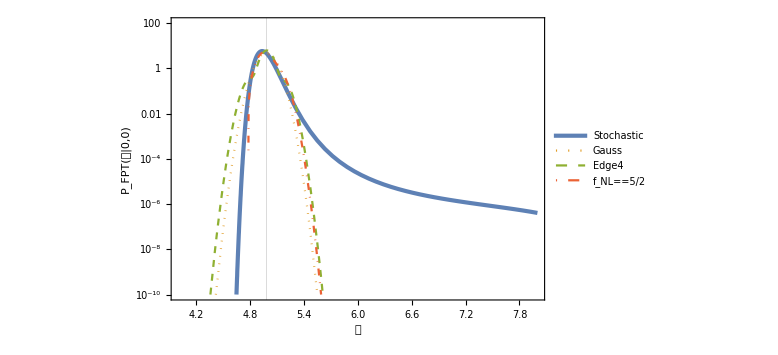

```mathematica
LogPlot[{FPFTint[NN],FPFTGauss[NN],FPFTEdge[NN],FPFTEdgefNL[NN]},{NN,4,8},PlotStyle->{AbsoluteThickness[3],Dotted,Dashed,DotDashed},PlotRange->{10^-10,10^2},FrameLabel->{𝒩,Subscript[P, FPT][𝒩|0,0]},GridLines->{{Nmean},None},PlotLegends->Placed[LineLegend[{"Stochastic","Gauss","Edge4",Subscript[f, NL]==5/2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.75,0.75}]]
```

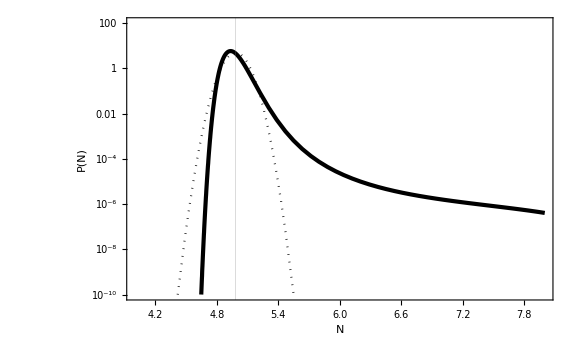

```mathematica
LogPlot[{FPFTint[NN],FPFTGauss[NN]},{NN,4,8},PlotStyle->{{AbsoluteThickness[3],Black},{Dotted,Black}},PlotRange->{10^-10,10^2},FrameLabel->{N,P[N]},GridLines->{{Nmean},None}]
```

```mathematica
FPFTint[Nmean+1]//ScientificForm
```

2.60123×10^-5

```mathematica
Ndrop=NN/.FindRoot[FPFTint[NN]==10^-9,{NN,7.4}]
```

7.5279

General::munfl: Exp[-3672.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2130.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3672.22] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

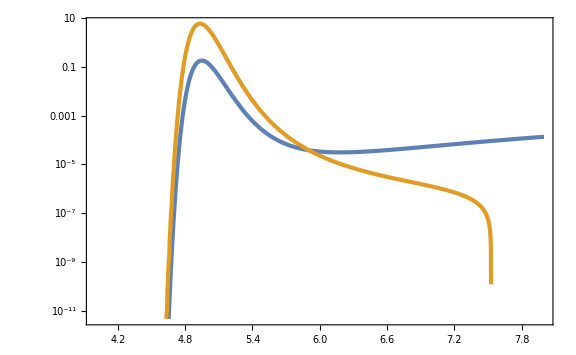

```mathematica
LogPlot[{P0[B[NN],NN],FPFTint[NN]},{NN,4,8}]
```

```mathematica
NIntegrate[FPFTGauss[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTGauss[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTGauss[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTGauss[NN],{NN,Nmin,Nmax}]/Z3
```

1.

1.

1.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NN near {NN} = {4.953}. NIntegrate obtained 8.2393×10^-20 and 5.22182×10^-19 for the integral and error estimates.

1.25446×10^-15

```mathematica
NIntegrate[FPFTEdge[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTEdge[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTEdge[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTEdge[NN],{NN,Nmin,Nmax}]/Z3
(NIntegrate[(NN-Nmean)^4 FPFTEdge[NN],{NN,Nmin,Nmax}]-3 varZ^2)/Z4
```

1.

1.

1.

«2 more identical outputs»

```mathematica
B[4]//N
```

171.446

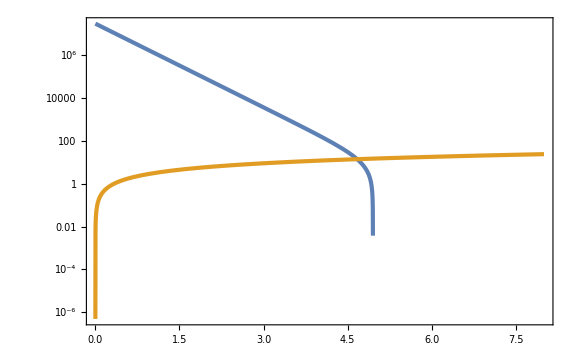

```mathematica
LogPlot[{B[NN],3NN},{NN,Nmin,Nmax}]
```

```mathematica
xmin=-20;
xmax=3NN/.FindRoot[B[NN]==3NN,{NN,4.5}]
```

14.0035

```mathematica
B[8]//N
```

-10.5398

```mathematica
PFP[x_,NN_]:=P0[x,NN]-NIntegrate[FPFTint[Np]P0[x-B[Np],NN-Np],{Np,0,NN}]/;x<B[NN]
PFP[x_,NN_]:=0/;x≥B[NN]
```

```mathematica
PFP[0,5]
```

0

```mathematica
PFPList=Flatten[ParallelTable[{x,NN,PFP[x,NN]//Quiet},{NN,Nmin+1/10,Nmax,1/10},{x,-3 Nmax,xmax,1/10}],1];//AbsoluteTiming
```

{2468.71,Null}

```mathematica
Export["PFPList.dat",PFPList];
```

```mathematica
PFPList=Import["PFPList.dat"]//ToExpression;
```

```mathematica
PFPList[[1]]
```

{-24,1/10,0.}

```mathematica
PFPint[x_,NN_]=Interpolation[PFPList,InterpolationOrder->1][x,NN];
```

```mathematica
ColorData[10,"ColorList"]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}

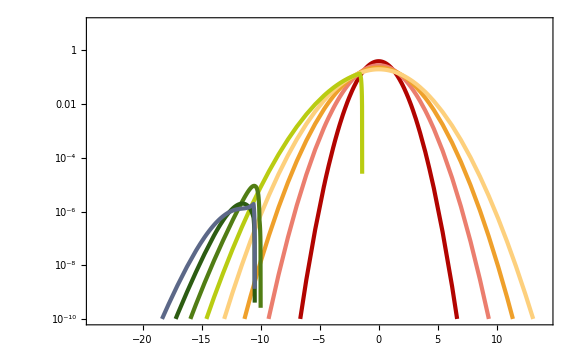

```mathematica
LogPlot[{PFPint[x,1],PFPint[x,2],PFPint[x,3],PFPint[x,4],PFPint[x,5],PFPint[x,6],PFPint[x,7],PFPint[x,8]},{x,-3 Nmax,xmax},PlotRange->{10^-10,10},PlotStyle->Map[{AbsoluteThickness[3],#}&,ColorData[10,"ColorList"]]]
```

```mathematica
NB[x_]=InverseFunction[B][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/3 Log[(20000000 √2 π)/(10 √10+3 x)]

```mathematica
FigPFP=Show[ContourPlot[Log10[Max[PFPint[x,NN],10^-20]],{x,-3Nmax,xmax},{NN,Nmin,Nmax},PlotRange->{{-20,xmax},{Nmin,Nmax},{-10,2}},Contours->11,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 P(z, 𝔑)",Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑}],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

InterpolatingFunction::dmval: Input value {-23.9973,0.000571429} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["../FigPFP.pdf",FigPFP];
```

```mathematica
N1List=Import["c++/Mn_USRzetaR.dat"];(*Select[Import["c++/Mn_USRzetaR.dat"],0≤#[[2]]≤8&];*)
```

```mathematica
FigN1=Show[ListContourPlot[N1List,PlotRange->{{-15,10},{Nmin,Nmax}},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[⟨N⟩,Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑},Contours->14],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

-Graphics-

```mathematica
Export["../FigN1.pdf",FigN1];
```

```mathematica
N1int[x_,NN_]=Interpolation[N1List][x,NN];
```

```mathematica
NmFP=N1int[0,0]
```

5.00236

```mathematica
N1x[x_,NN_]=D[N1int[x,NN], x];
```

```mathematica
Show[ContourPlot[N1x[x,NN],{x,-17,10},{NN,0,8},PlotLegends->BarLegend[Automatic,LegendLabel->Placed[⟨N⟩,Right,Rotate[#,-90Degree]&]],FrameLabel->{z,𝔑}],Plot[NB[x],{x,-10Sqrt[10]/3,20},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top,PlotRange->{4,10}]]
```

-Graphics-

#### Nbw = 3

```mathematica
Nbw=3;
```

```mathematica
NLists=Table[NN,{NN,Nmin,Nbw,DN}];
Length[NLists]
```

301

```mathematica
Bs[NN_,xxs_,NNs_]=(2π xf)/H-xxs-(2π dotx0)/(3 H^2)(1-E^(-3(NN+NNs)))//Simplify;
g1s[NN_,xxs_,NNs_]=Simplify[(Bs[NN,xxs,NNs]/NN-2 D[Bs[NN,xxs,NNs], NN])P0[Bs[NN,xxs,NNs],NN]]
g2s[N1_,N2_,xxs_,NNs_]=Simplify[(2 D[Bs[N1,xxs,NNs], N1]-(Bs[N1,xxs,NNs]-Bs[N2,xxs,NNs])/(N1-N2))P0[Bs[N1,xxs,NNs]-Bs[N2,xxs,NNs],N1-N2]]
```

(ⅇ^(-3 NN-3 NNs-(((10 √10)/3-20000000/3 √2 ⅇ^(-3 (NN+NNs)) π+xxs)^2)/(2 NN)) (20000000 √2 (1+6 NN) π-ⅇ^(3 (NN+NNs)) (10 √10+3 xxs)))/(3 NN^(3/2) √(2 π))

(20000000 ⅇ^(-3 N1-3 N2-3 NNs-(400000000000000 ⅇ^(-6 (N1+N2+NNs)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
PbwList=Flatten[ParallelTable[{xs,Ns,
If[Bs[0,xs,Ns]≤0,0,
Deltas[xs,Ns]=Table[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2s[NLists[[i]],Np,xs,Ns],{Np,NLists[[i]]-DN,NLists[[i]]}]]//Quiet,N[DN/2 g2s[NLists[[i]],NLists[[j]]-DN/2,xs,Ns]]//Quiet]],{i,Length[NLists]},{j,Length[NLists]}];
FPFTLists[1,xs,Ns]=0;
FPFTLists[2,xs,Ns]=g1s[NLists[[2]],xs,Ns](1-Deltas[xs,Ns][[2,2]])^-1//Quiet;
For[i=3,i≤Length[NLists],i++,
FPFTLists[i,xs,Ns]=(1-Deltas[xs,Ns][[i,i]])^-1(g1s[NLists[[i]],xs,Ns]+Sum[FPFTLists[j,xs,Ns](Deltas[xs,Ns][[i,j]]+Deltas[xs,Ns][[i,j+1]])//Quiet,{j,2,i-1}])//Quiet;];
FPFTLists[Length[NLists],xs,Ns]PFPint[xs,Ns]
]},{Ns,Nmin+1/10,Nmax,1/10},{xs,-3 Nmax,xmax,1/10}],1];//AbsoluteTiming
```

General::munfl: 5.5252×10^-308 0.0872845 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.51721×10^-308 2.9749×10^-70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.22084×10^-307 1.33803×10^-69 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{44107.,Null}

```mathematica
48600/3600//N
```

13.5

```mathematica
Export["Pbw.dat",PbwList];
```

```mathematica
PbwList=Import["Pbw.dat"]//ToExpression;
```

```mathematica
ListContourPlot[PbwList]
```

-Graphics-

```mathematica
LogPbwList=Map[{#[[1]],#[[2]],If[#[[3]]≤10^-20,-20,Log10[#[[3]]]]}&,PbwList,1];
```

```mathematica
FigPbw=Show[ListContourPlot[LogPbwList,PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 P_bw(z, 𝔑; N_bw = 3)",Right,Rotate[#,-90Degree]&]],PlotRange->{{-17,10},{1.5,8},{-10,2}},Contours->11,FrameLabel->{z,𝔑}],Plot[NB[x],{x,-10 Sqrt[10]/3,12},PlotRange->{4,9},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top]]
```

-Graphics-

```mathematica
Export["../FigPbw.pdf",FigPbw];
```

```mathematica
Pbwint[x_,NN_]=Interpolation[PbwList][x,NN];
```

```mathematica
FindRoot[zetaR==Ns-NmFP+N1int[xs,Ns]/.{zetaR->3,Ns->2.8},{xs,Min[-1,B[Ns]-1/100]}/.{zetaR->3,Ns->2.8}]
```

InterpolatingFunction::dmval: Input value {-21.,2.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-43.,2.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

{xs→-8.55715}

```mathematica
zmin=-1/5;
zmax=3;
```

```mathematica
xs3List=Flatten[ParallelTable[{zetaR,Ns,If[zetaR-Ns+NmFP>0,xs/.FindRoot[zetaR==Ns-NmFP+N1int[xs,Ns],{xs,Min[-1,B[Ns]-1/100]}]//Quiet,B[Ns]]},{zetaR,zmin,zmax,1/100},{Ns,Nmin,Nmax,1/10}],1];//AbsoluteTiming
```

{24.3816,Null}

```mathematica
xs3int[zetaR_,Ns_]=Interpolation[xs3List,InterpolationOrder->1][zetaR,Ns];
```

```mathematica
PR3integrandxN[xs_,Ns_]:=Pbwint[xs,Ns]/Abs[N1x[xs,Ns]]/;xs<B[Ns]
PR3integrandxN[xs_,Ns_]:=0/;xs≥B[Ns]
```

```mathematica
PR3integrandxNList=Flatten[ParallelTable[{xs,Ns,PR3integrandxN[xs,Ns]},{xs,xmin,xmax,1/10},{Ns,Nmin+1/10,Nmax,1/10}],1];//AbsoluteTiming
```

General::munfl: 1.22989×10^-307 0.140614 is too small to represent as a normalized machine number; precision may be lost.

{2.52956,Null}

```mathematica
PR3integrandxNLogList=Map[{#[[1]],#[[2]],If[#[[3]]≥10^-20,Log10[#[[3]]],-20]}&,PR3integrandxNList];
```

```mathematica
FigPR3integrand=Show[ListContourPlot[PR3integrandxNLogList,PlotRange->{{-17,10},{1.5,8},{-10,2}},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10 (P_bw(z, 𝔑; N_bw = 3))/(|∂⟨𝒩⟩/∂z_*|)",Right,Rotate[#,-90Degree]&]],Contours->11,FrameLabel->{z,𝔑}],ParametricPlot[{{xs3int[-1/5,Ns],Ns},{xs3int[-1/10,Ns],Ns},{xs3int[0,Ns],Ns},{xs3int[1/10,Ns],Ns},{xs3int[1/5,Ns],Ns},{xs3int[1/2,Ns],Ns},{xs3int[1,Ns],Ns},{xs3int[2,Ns],Ns},{xs3int[3,Ns],Ns}},{Ns,Nmin,Nmax},PlotStyle->Map[{AbsoluteThickness[2],Dashed,#}&,ColorData[10,"ColorList"]]],Plot[NB[x],{x,-10 Sqrt[10]/3,12},PlotRange->{4,9},PlotStyle->{AbsoluteThickness[3],ColorData[97,"ColorList"][[4]]},Filling->Top]]
```

-Graphics-

```mathematica
Export["../FigPR3integrand.pdf",FigPR3integrand];
```

```mathematica
PR3integrand[zetaR_,Ns_]:=Pbwint[xs3int[zetaR,Ns],Ns]/Abs[N1x[xs3int[zetaR,Ns],Ns]]/;zetaR-Ns+NmFP≥0
PR3integrand[zetaR_,Ns_]:=0/;zetaR-Ns+NmFP<0
```

```mathematica
PR3integrand[13/50,4]
```

1.06584×10^-6

```mathematica
Pbwint[xs3int[zetaR,Ns],Ns]/Abs[N1x[xs3int[zetaR,Ns],Ns]]/.{zetaR->0,Ns->4}
```

-7.24974×10^-9

```mathematica
PR3[zetaR_]:=NIntegrate[PR3integrand[zetaR,Ns],{Ns,Nmin,Nmax},WorkingPrecision->10]
```

```mathematica
PR3[13/50]
```

0.007006874576

```mathematica
PR3List=Table[{zetaR,PR3[zetaR]//Quiet},{zetaR,zmin,zmax,1/100}];//AbsoluteTiming
```

{2.75976,Null}

```mathematica
PR3LogCut=Map[{#[[1]],Log[#[[2]]]}&,Select[PR3List,#[[1]]>1&]];
```

```mathematica
expPR3fit=FindFit[PR3LogCut,a-b x,{a,b},x]
exp3PR3fit=FindFit[PR3LogCut,a-b x-3 Log[x],{a,b},x]
expnPR3fit=FindFit[PR3LogCut,a-b x-n Log[x],{a,b,n},x]
```

{a→-10.63381628,b→1.6517928522}

{a→-11.849602857,b→0.071856126498}

{a→-12.48494691,b→-0.75378500185,n→4.5677358117}

```mathematica
PR3int[zetaR_]=Interpolation[PR3List][zetaR];
```

```mathematica
NIntegrate[PR3int[zetaR],{zetaR,-1/2,3/2}]
NIntegrate[zetaR PR3int[zetaR],{zetaR,-1/2,3/2}]
var3=NIntegrate[zetaR^2 PR3int[zetaR],{zetaR,-1/2,3/2}]
k33=NIntegrate[zetaR^3 PR3int[zetaR],{zetaR,-1/2,3/2}]
NIntegrate[zetaR^4 PR3int[zetaR],{zetaR,-1/2,3/2}]-3 var3^2
```

InterpolatingFunction::dmvali: The integration endpoint -1/2 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.987512861

0.0101819

-0.00173843

0.00190528

-0.000799637

```mathematica
5/18 k33/var3^2
```

175.122

InterpolatingFunction::dmval: Input value {-0.499929} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

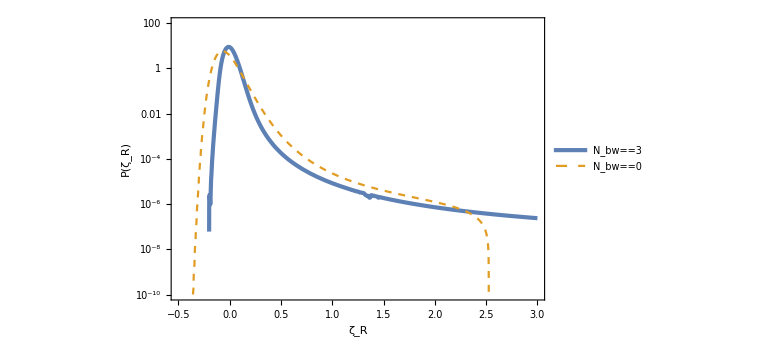

```mathematica
LogPlot[{PR3int[zeta],FPFTint[NmFP+zeta]},{zeta,-1/2,zmax},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted,DotDashed},FrameLabel->{Subscript[ζ, R],P[Subscript[ζ, R]]},PlotLegends->Placed[{Subscript[N, bw]==3,Subscript[N, bw]==0},{0.8,0.8}],PlotRange->{10^-10,10^2}]
```

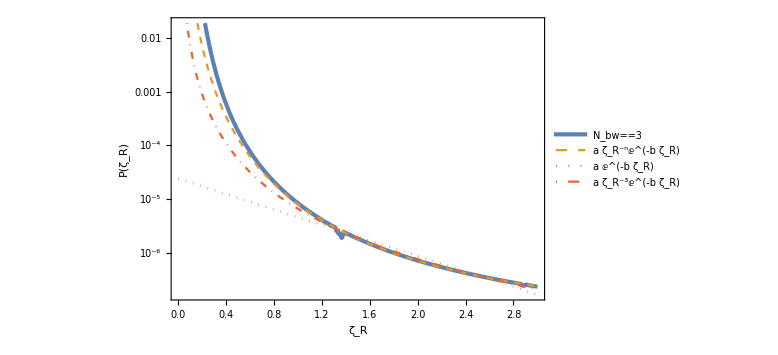

```mathematica
LogPlot[{PR3int[zeta],Exp[a] Exp[-b zeta]/zeta^n/.expnPR3fit,Exp[a]Exp[-b zeta]/.expPR3fit,Exp[a] Exp[-b zeta]/zeta^3/.exp3PR3fit},{zeta,0,zmax},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted,DotDashed},FrameLabel->{Subscript[ζ, R],P[Subscript[ζ, R]]},PlotLegends->Placed[LineLegend[{Subscript[N, bw]==3,Row[{a," ζ_R^-n",Exp[-b Subscript[ζ, R]]}],a Exp[-b Subscript[ζ, R]],Row[{a," ζ_R^-3",,Exp[-b Subscript[ζ, R]]}]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.75,0.7}]]
```

### C++

```mathematica
chiList=Import["c++/chi_USRchiN.dat"];
```

```mathematica
chiList[[1]]
```

{-20,0,0,0.999998}

```mathematica
ITNo=(Length[chiList[[1]]]-2)/2
```

1

```mathematica
chiinvList=Flatten[Table[{chiList[[i,1]],chiList[[i,2]],chiList[[i,1+2j]],1/chiList[[i,2+2j]]},{i,Length[chiList]},{j,ITNo}],1];
```

```mathematica
chiinvList[[1]]
```

{-20,0,0,1.}

```mathematica
chiinvint[xs_,Ns_,it_]=Interpolation[chiinvList][xs,Ns,it];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,3,0}.

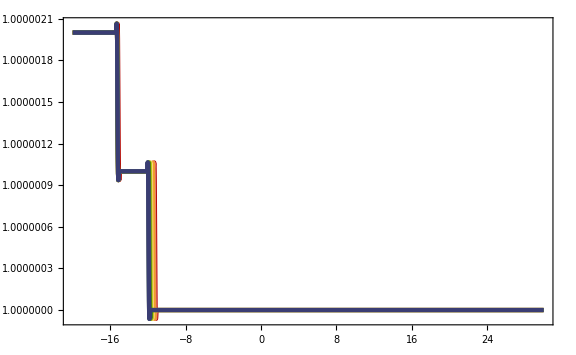

```mathematica
Plot[{chiinvint[xs,0,0],chiinvint[xs,1,0],chiinvint[xs,2,0],chiinvint[xs,3,0],chiinvint[xs,4,0],chiinvint[xs,5,0],chiinvint[xs,6,0],chiinvint[xs,7,0],chiinvint[xs,8,0]},{xs,-20,30},PlotRange->Full,PlotStyle->Map[{AbsoluteThickness[3],#}&,ColorData[10,"ColorList"]]]
```

```mathematica
xs=-11;
Ns=Nmax;Ns//N
```

8.

```mathematica
Bs[NN_]=(2π xf)/H-xs-(2π dotx0)/(3 H^2)(1-E^(-3(NN+Ns)));
```

```mathematica
Bs[0]//N
```

0.460193

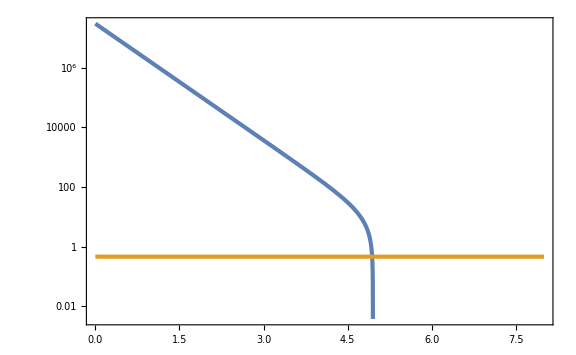

```mathematica
LogPlot[{B[NN],Bs[NN]},{NN,Nmin,Nmax}]
```

```mathematica
g1s[NN_]=(Bs[NN]/NN-2Bs'[NN])P0[Bs[NN],NN]//Simplify
g2s[N1_,N2_]=(2Bs'[N1]-(Bs[N1]-Bs[N2])/(N1-N2))P0[Bs[N1]-Bs[N2],N1-N2]//Simplify
```

1/(3 NN^(3/2) √(2 π))ⅇ^(-(ⅇ^(-6 (8+NN)) (ⅇ^(6 (8+NN)) (2089-660 √10+432 NN+54 NN^2)+40000000 (33 √2-20 √5) ⅇ^(3 (8+NN)) π+800000000000000 π^2))/(18 NN)) ((33-10 √10) ⅇ^(3 (8+NN))+20000000 √2 (1+6 NN) π)

(20000000 ⅇ^(-24-3 N1-3 N2-(400000000000000 ⅇ^(-6 (8+N1+N2)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
NLists=Table[NN,{NN,Nmin,Nbw,DN}];
Length[NLists]
```

301

```mathematica
Deltas=Table[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2s[NLists[[i]],Np],{Np,NLists[[i]]-DN,NLists[[i]]}]]//Quiet,N[DN/2 g2s[NLists[[i]],NLists[[j]]-DN/2]]//Quiet]],{i,Length[NLists]},{j,Length[NLists]}];//AbsoluteTiming
```

{29.9512,Null}

```mathematica
FPFTLists=Table[0,{i,Length[NLists]}];
```

```mathematica
FPFTLists[[1]]={NLists[[1]],0};
FPFTLists[[2]]={NLists[[2]],g1s[NLists[[2]]](1-Deltas[[2,2]])^-1}//Quiet;
For[i=3,i≤Length[FPFTLists],i++,
FPFTLists[[i]]={NLists[[i]],(1-Deltas[[i,i]])^-1(g1s[NLists[[i]]]+Sum[FPFTLists[[j,2]](Deltas[[i,j]]+Deltas[[i,j+1]])//Quiet,{j,2,i-1}])}//Quiet;]//AbsoluteTiming
```

{2.47389,Null}

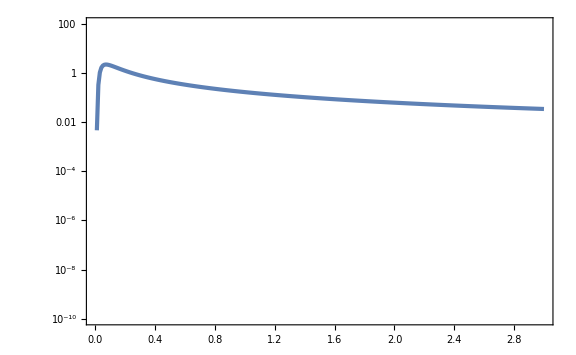

```mathematica
ListLogPlot[FPFTLists,PlotRange->{10^-10,10^2}]
```

```mathematica
Last[FPFTLists]
```

{3,0.0340606}

```mathematica
PFP6List=ParallelTable[{x,PFP[x,6]//Quiet},{x,-3 6,B[6],1/100}];//AbsoluteTiming
```

{66.6572,Null}

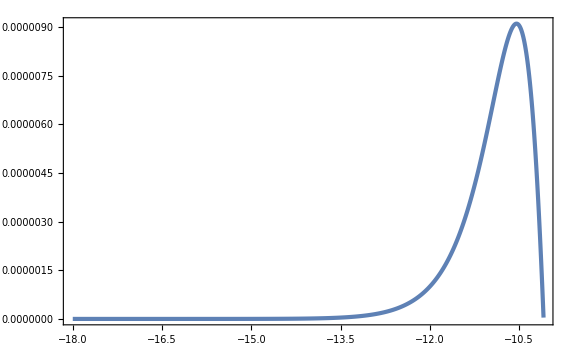

```mathematica
ListPlot[PFP6List,PlotRange->Full]
```

```mathematica
PFP6int[x_]=Interpolation[PFP6List][x];
```

```mathematica
NIntegrate[PFP6int[x],{x,-3 6,B[6]}]
```

InterpolatingFunction::dmvali: The integration endpoint -20000000/3 √2 (1-1/ⅇ^18) π+20000000000000000/3 (1/(500000000 √2)-1/(200000000000000 √10 π)) π in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

9.92386×10^-6

```mathematica
BR[NN_,NR_]=B[NN+NR];
```

```mathematica
g1R[NN_,NR_]=(BR[NN,NR]/NN-2 D[BR[NN,NR], NN])P0[BR[NN,NR],NN]//Simplify
g2R[N1_,N2_,NR_]=(2 D[BR[N1,NR], N1]-(BR[N1,NR]-BR[N2,NR])/(N1-N2))P0[BR[N1,NR]-BR[N2,NR],N1-N2]//Simplify
```

(ⅇ^(-(500+27 NN^2+27 NN NR-400000000 √5 ⅇ^(-3 (NN+NR)) π+400000000000000 ⅇ^(-6 (NN+NR)) π^2)/(9 NN)) (-10 √5 ⅇ^(3 (NN+NR))+20000000 (π+6 NN π)))/(3 NN^(3/2) √π)

(20000000 ⅇ^(-3 N1-3 N2-3 NR-(400000000000000 ⅇ^(-6 (N1+N2+NR)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
DN=1/100;
NRList=Table[NN,{NN,3-NR,11-NR,DN}]/.{NR->3};
Length[NRList]
```

801

```mathematica
DeltaR=ParallelTable[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2R[NRList[[i]],Np,NR]/.{NR->3},{Np,NRList[[i]]-DN,NRList[[i]]}]]//Quiet,N[DN/2 g2R[NRList[[i]],NRList[[j]]-DN/2,NR]/.{NR->3}]//Quiet]],{i,Length[NRList]},{j,Length[NRList]}];//AbsoluteTiming
```

{12.9626,Null}

```mathematica
FPFTRList=Table[0,{i,Length[NRList]}];
```

```mathematica
FPFTRList[[1]]={NRList[[1]],0};
FPFTRList[[2]]={NRList[[2]],g1R[NRList[[2]],NR](1-DeltaR[[2,2]])^-1/.{NR->3}}//Quiet;
For[i=3,i≤Length[FPFTRList],i++,
FPFTRList[[i]]={NRList[[i]],(1-DeltaR[[i,i]])^-1(g1R[NRList[[i]],NR]+ParallelSum[FPFTRList[[j,2]](DeltaR[[i,j]]+DeltaR[[i,j+1]])//Quiet,{j,2,i-1}])/.{NR->3}}//Quiet;]//AbsoluteTiming
```

{30.2999,Null}

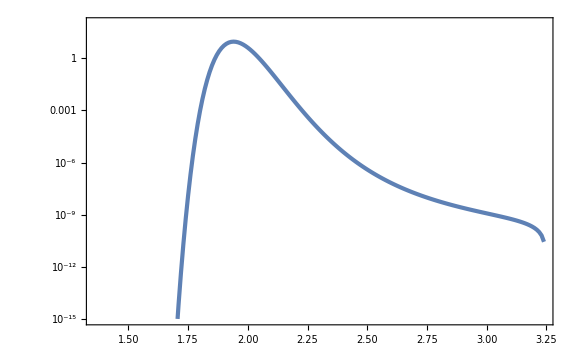

```mathematica
ListLogPlot[FPFTRList,PlotRange->{10^-15,10^2}]
```

```mathematica
NminR=1.5;
NmaxR=4;
```

```mathematica
FPFTRint[NN_]=Interpolation[FPFTRList,InterpolationOrder->1][NN];
```

```mathematica
NIntegrate[FPFTRint[NN],{NN,NminR,NmaxR}]
NmeanR=NIntegrate[NN FPFTRint[NN],{NN,NminR,NmaxR}]
varZR=NIntegrate[(NN-NmeanR)^2 FPFTRint[NN],{NN,NminR,NmaxR}]
Z3R=NIntegrate[(NN-NmeanR)^3 FPFTRint[NN],{NN,NminR,NmaxR}]
Z4R=NIntegrate[(NN-NmeanR)^4 FPFTRint[NN],{NN,NminR,NmaxR}]-3 varZR^2
fNLR=5/18 Z3R/varZR^2
```

1.00363

1.95776

0.00213992

4.4585×10^-6

1.28613×10^-6

0.270454

```mathematica
Nf-NR/.{NR->3}//N
```

1.94956

```mathematica
H3[x_]=x^3-3x;
H4[x_]=x^4-6 x^2+3;
```

```mathematica
Z3RfNL=18/5 varZR^2 5/2
```

0.0000412131

```mathematica
Nmean
```

4.97525

```mathematica
FPFTRGauss[NN_]=1/Sqrt[2π varZR] Exp[(-(NN-NmeanR)^2)/(2varZR)];
FPFTREdge[NN_]=(1+1/(3 2)Z3R/varZR^(3/2)H3[(NN-NmeanR)/Sqrt[varZR]]+1/(4 3 2)Z4R/varZR^2 H4[(NN-NmeanR)/Sqrt[varZR]])FPFTRGauss[NN];
FPFTREdgefNL[NN_]=(1+1/(3 2)Z3RfNL/varZR^(3/2)H3[(NN-NmeanR)/Sqrt[varZR]])FPFTRGauss[NN];
```

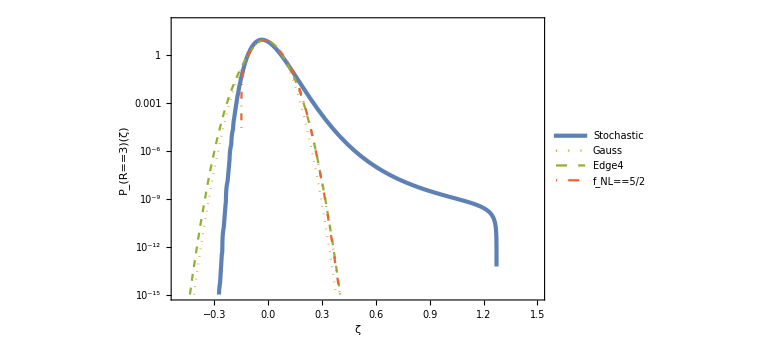

```mathematica
LogPlot[{FPFTRint[zeta+Nmean-NR]/.{NR->3},FPFTRGauss[zeta+Nmean-NR]/.{NR->3},FPFTREdge[zeta+Nmean-NR]/.{NR->3},FPFTREdgefNL[zeta+Nmean-NR]/.{NR->3}},{zeta,-0.5,1.5},PlotStyle->{AbsoluteThickness[3],Dotted,Dashed,DotDashed},PlotRange->{10^-15,10^2},FrameLabel->{ζ,Subscript[P, R==3][ζ]},PlotLegends->Placed[LineLegend[{"Stochastic","Gauss","Edge4",Subscript[f, NL]==5/2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.75,0.75}]]
```

```mathematica
FPFTRint[1+Nmean-NR]/.{NR->3}
```

1.42415×10^-9

```mathematica
varZ/Nmean
varZR/NmeanR
```

0.00124708

0.00109305

```mathematica
PR[zeta_,NR_]:=PFP[B[zeta+Nf],zeta+Nf-NR]
```

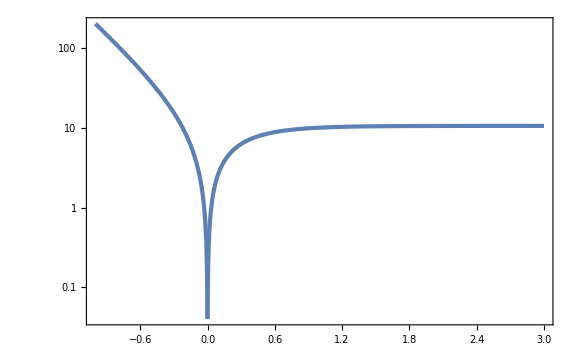

```mathematica
LogPlot[Abs[B[zeta+Nf]],{zeta,-1,3},PlotRange->Full]
```

```mathematica
zetamin[NR_]=NR-Nf;
```

```mathematica
zetamin[3]//N
```

-1.94956

```mathematica
PR[10,3]//Quiet
```

5.24715×10^-6

```mathematica
PR3List=ParallelTable[{zeta,PR[zeta,3]//Quiet},{zeta,-1,3,1/100}];//AbsoluteTiming
```

{20.6656,Null}

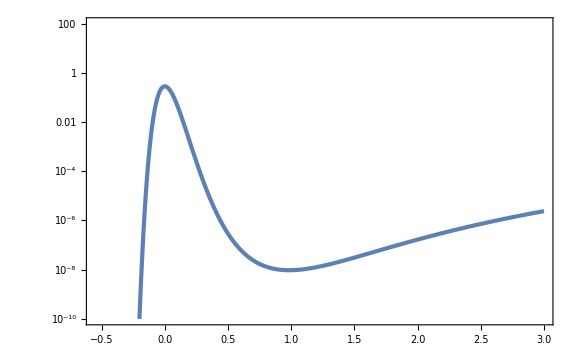

```mathematica
ListLogPlot[PR3List,PlotRange->{10^-10,10^2}]
```

```mathematica
PR3int[zeta_]=Interpolation[PR3List,InterpolationOrder->1][zeta];
```

```mathematica
Norm3=NIntegrate[PR3int[zeta],{zeta,-1,3}]
```

General::munfl: 1.29646×10^-306 (-0.01) is too small to represent as a normalized machine number; precision may be lost.

0.032382

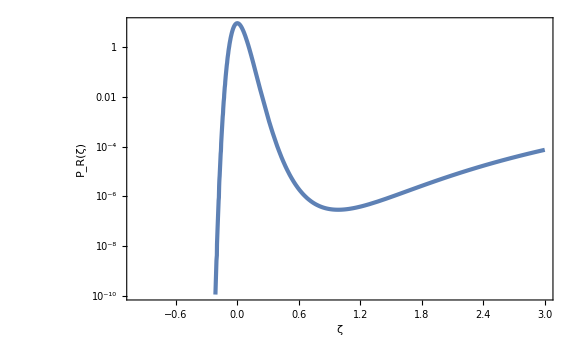

```mathematica
LogPlot[1/Norm3 PR3int[zeta],{zeta,-1,3},FrameLabel->{{Subscript[P, R][ζ],None},{ζ,Subscript[N, bw][R]==3}}]
```

```mathematica
zetamin[0]//N
```

-4.94956

```mathematica
PR[5,0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Np near {Np} = {5.13009}. NIntegrate obtained 0.000473562 and 1.96354×10^-8 for the integral and error estimates.

1.80601×10^-6

```mathematica
PR0List=ParallelTable[{zeta,PR[zeta,0]//Quiet},{zeta,-1,3,1/100}];//AbsoluteTiming
```

{102.387,Null}

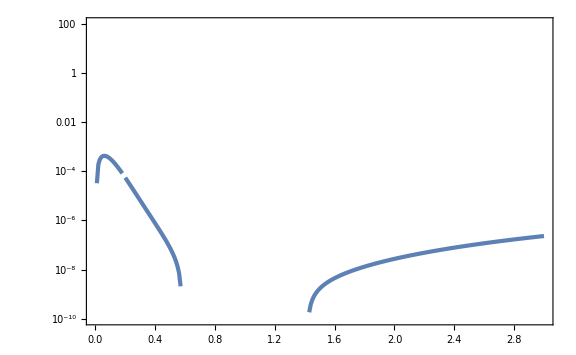

```mathematica
ListLogPlot[PR0List,PlotRange->{10^-10,10^2}]
```

```mathematica
C/Sqrt[S-(S-dS/2)]
1/(Sqrt[2]dS)Integrate[C/Sqrt[S-Sp],{Sp,S-dS,S}]
Integrate[1/Sqrt[S-Sp],{Sp,S-dS,S}]
```

(√2 C)/(√dS)

(√2 C)/(√dS)

2 √dS